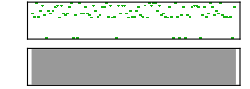

```mathematica
rule=ArrayRules[ToString/@{C,D,E,F5,G,A1,B3,C5,D5,C3}];
length=Sound[SoundNote@@@Table[{{RealDigits[N[Pi,#]][[1,i]]},.46,"NewAge"},{i,#}]/.rule]&;
length[100]
```

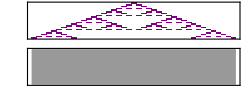

```mathematica
Sound[SoundNote[DeleteCases[3 Range[21]Reverse[#],0]-24,.1]&/@Transpose[CellularAutomaton[90,{{1},0},20]]]
```

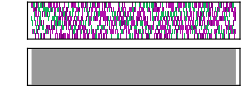

```mathematica
Sound[Table[SoundNote[RandomInteger[7],.2,RandomChoice[{"Piano","Guitar","Violin"}]],1000]]
```